```mathematica
ClearAll["Global`*"]
```

```mathematica
(* set your home directory *)
SetDirectory[NotebookDirectory[]];
```

# Wave Interference Example Animation

## Mesh

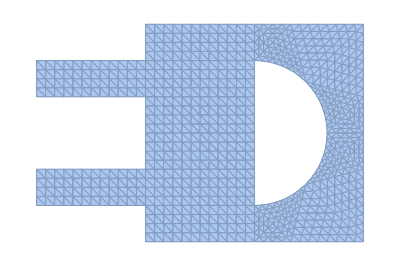

```mathematica
nodes=Import["nodes.dat","Table"];
nodeCount=Length@nodes;
triangles=Import["triangles.dat","Table"]+1;
𝒦=MeshRegion[nodes,Triangle/@triangles]
HighlightMesh[𝒦,0,MeshCellLabel->{0->"Index"}];
```

```mathematica
MeshCellCount[𝒦,0]
```

800

```mathematica
(*
matrix=Import["m.dat","Table"];
MatrixPlot@matrix
*)
```

### Boundary

```mathematica
G1=Import["G1.dat","List"]+1;
G2=Import["G2.dat","List"]+1;
HighlightMesh[𝒦,0,MeshCellHighlight->{{0,G1}->Red,{0,G2}->Purple}]
```

-Graphics-

## Soln

```mathematica
time=Import["time.dat","List"];
timeCount=Length@time;
```

```mathematica
ξ=Chop@Import["xi.dat","Table"];
```

```mathematica
Do[Subscript[u, m]=Interpolation[Table[{nodes[[i]],ξ[[m,i]]},{i,nodeCount}],InterpolationOrder->1],{m,timeCount}]
```

```mathematica
waveFrames=Table[Plot3D[Subscript[u, m][x,y],{x,y}∈𝒦,PlotLabel->"t = "<>ToString[time[[m]]],PlotRange->{-.1,.1},Axes->None,Mesh->False,Boxed->False],{m,timeCount}];
```

```mathematica
Manipulate[waveFrames[[m]],{{m,1,"time frame"},1,timeCount,1}]
```